# Bad

## 1. Single qubit

```mathematica
Clear["Global`*"]
```

```mathematica
$Assumptions=Abs[α]^2+Abs[β]^2==1
```

Abs[α]^2+Abs[β]^2==1

#### Operators and states

```mathematica
E0[p_]:=({{1, 0}, {0, √(1-p)}});
E1[p_]:=({{0, √p}, {0, 0}});
X=({{0, 1}, {1, 0}});
ψ0={α,β};
ψ0s={SuperStar[α],SuperStar[β]};
ρ0=({{Abs[α]^2, α SuperStar[β]}, {SuperStar[α] β, Abs[β]^2}});
```

#### Ideal reversal

```mathematica
X.E0[p2].X.E0[d].E0[p1]//MatrixForm
```

(√(1-p2) | 0
0 | √(1-d) √(1-p1))

So √(1-p2)=√(1-d)√(1-p1)

#### Evolution

```mathematica
(*ρ1=Simplify[E0[p1].ρ0.Transpose[E0[p1]]+η E1[p1].ρ0.Transpose[E1[p1]],0<p1<1];*)
ρd=Simplify[E0[d].ρ0.Transpose[E0[d]]+ E1[d].ρ0.Transpose[E1[d]],0<p1<1];
ρd//MatrixForm
```

(Abs[α]^2+d Abs[β]^2 | √(1-d) α β^*
√(1-d) β α^* | -(-1+d) Abs[β]^2)

```mathematica
ρr=Simplify[X.E0[p].X.ρd.Transpose[X.E0[p].X]+ η X.E1[p].X.ρd.Transpose[X.E1[p].X],0<p1<1];
ρr=ρr/.{p->d};
ρr//MatrixForm
```

(-(-1+d) (Abs[α]^2+d Abs[β]^2) | (1-d) α β^*
(1-d) β α^* | d η Abs[α]^2+(1+d (-1+d η)) Abs[β]^2)

```mathematica
Tr[ρr]//Simplify
```

(1+d (-1+η)) Abs[α]^2+(1+d^2 (-1+η)) Abs[β]^2

#### Fidelity

```mathematica
f=ψ0s.ρr.ψ0//Simplify
```

β (d η Abs[α]^2+(1+d (-1+d η)) Abs[β]^2-(-1+d) α α^*) β^*-(-1+d) α α^* (Abs[α]^2+d Abs[β]^2+β β^*)

#### Conclusion:

```mathematica
R[d_]:=1-d;
S[d_,ηb_,β2_]:=(1+ηb d/(1-d)+d(1-ηb)β2)^-1;
```

```mathematica
Fd[d_]:=
```

```mathematica
ρ1//MatrixForm
```

(Abs[α]^2+p1 η Abs[β]^2 | √(1-p1) α β^*
√(1-p1) β α^* | -(-1+p1) Abs[β]^2)

```mathematica
ρ2//MatrixForm
```

(Abs[α]^2+(d-d p1+p1 η) Abs[β]^2 | √((-1+d) (-1+p1)) α β^*
√((-1+d) (-1+p1)) β α^* | (-1+d) (-1+p1) Abs[β]^2)

```mathematica
ρ3//MatrixForm
```

((1-d) (1-p1) (Abs[α]^2+(d-d p1+p1 η) Abs[β]^2) | √((1-d) (1-p1)) √((-1+d) (-1+p1)) α β^*
√((1-d) (1-p1)) √((-1+d) (-1+p1)) β α^* | (-1+d) (-1+p1) Abs[β]^2+(1-(1-d) (1-p1)) η (Abs[α]^2+(d-d p1+p1 η) Abs[β]^2))

Normalization factor

```mathematica
Tr[ρ3]//Simplify
```

(-1+d) (-1+p1) Abs[β]^2+(1-d) (1-p1) (Abs[α]^2+(d-d p1+p1 η) Abs[β]^2)+(d+p1-d p1) η (Abs[α]^2+(d-d p1+p1 η) Abs[β]^2)

#### Detection efficiency

```mathematica
A[p1_,d_,η_,β_]:=Abs[β]^2+η(1-η+η/((1-d)(1-p1)))(1+(d-1)Abs[β]^2+(η-d)Abs[β]^2 p1)
```

```mathematica
DA[p1_,d_,η_,β_]:=D[A[p1,d,η,β]^-1,{p1,1}]
```

```mathematica
DA[p1,d,η,β]//FullSimplify
```

(η (η+β (-1+η) (-d^2 (-1+p1)^2-(-2+p1) p1 η+d (-1+p1)^2 (1+η)) Conjugate[β]))/((-1+d) (-1+p1)^2 (Abs[β]^2+η (1+(-1+1/((-1+d) (-1+p1))) η) (1+β (-1+d-d p1+p1 η) Conjugate[β]))^2)

```mathematica
DA[p1,d,η,β]/.p1->0//FullSimplify
```

((-1+d) η (η+d β (-1+d-d η+η^2) Conjugate[β]))/((1+d (-1+η)) η+(-1+d) β (-1+η) (1+d η) Conjugate[β])^2

```mathematica
Collect[η (η+d β (-1+d-d η+η^2) Conjugate[β]),η]
```

d β η^3 Conjugate[β]+η^2 (1-d^2 β Conjugate[β])+η (-d β Conjugate[β]+d^2 β Conjugate[β])

```mathematica
Collect[(d-1)η (η+d β (-1+d-d η+η^2) Conjugate[β]),η]
```

(-1+d) d β η^3 Conjugate[β]+(-1+d) η^2 (1-d^2 β Conjugate[β])+(-1+d) η (-d β Conjugate[β]+d^2 β Conjugate[β])

```mathematica
diffp1[d_,β_,η_]:=(d-1)Abs[β]^2 η(η^2-(d-1/(d Abs[β]^2))η+d-1)
```

```mathematica
poly[d_,β_,η_]:=η^2-(d-1/(d Abs[β]^2))η+d-1
```

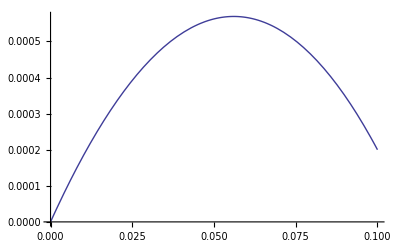

```mathematica
Plot[diffp1[0.8,1/(√2),η],{η,0,0.1}]
```

## 2. Single Qubit Reversal

```mathematica
Clear["Global`*"]
```

```mathematica
$Assumptions=Abs[α]^2+Abs[β]^2==1
```

Abs[α]^2+Abs[β]^2==1

### Reversibility, Success probability, Fidelity

```mathematica
R[p1_,d_]:=(1-d)(1-p1);
```

```mathematica
factor[p1_,d_]:=1/((1-d)(1-p1))-1;
```

```mathematica
A[β_,p1_,d_,η_]:=1+(d(1-p1)+η p1)Abs[β]^2+η factor[p1,d](1+(d-d p1+η p1-1)Abs[β]^2);
```

```mathematica
S[β_,p1_,d_,η_]:=1/A[β,p1,d,η]
```

```mathematica
Fr[β_,p1_,d_,η_]:=1/A[β,p1,d,η](1+((d-η)(1-p1)+η/(1-d)/(1-p1))(1-Abs[β]^2)Abs[β]^2+((η-d-η d)(1-p1)+η d/(1-d)-η^2 p1+η(η p1-1)/(1-d)(1-p1))Abs[β]^4);
```

### Example 1: β=1/√2,d=0.3

#### Reversibility and Success Probability

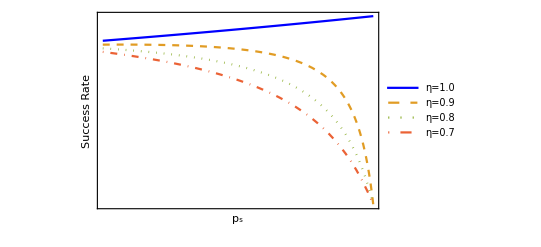

```mathematica
β=1/(√2);
d=0.3;
Plot[
{S[β,p1,d,0],
S[β,p1,d,0.1],
S[β,p1,d,0.2],
S[β,p1,d,0.3]},
{p1,0,1},
Frame->True,FrameLabel->{"p_s","Success Rate"},RotateLabel->True,FrameStyle->Directive[Black],
FrameTicks->{{None,All},{None,All}},
PlotLegends->Placed[LineLegend[{"η=1.0","η=0.9","η=0.8","η=0.7"},LegendLayout->{"Row",2}],{Left,Bottom}],
PlotStyle->{Blue, Dashed, Dotted, DotDashed},
BaseStyle->{FontFamily->"Times",FontSize->12}
]
```

```mathematica
?Placed
```

RowBox[{"Placed", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["pos", "TI"]}], "]"}] represents an expression StyleBox["expr", "TI"] placed at relative position StyleBox["pos", "TI"] in a chart or other display. 
RowBox[{"Placed", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["e", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["e", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["pos", "TI"]}], "]"}] places each of the SubscriptBox[StyleBox["e", "TI"], StyleBox["i", "TI"]] at a relative position specified by StyleBox["pos", "TI"].
RowBox[{"Placed", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["e", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["e", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["pos", "TI"], ",", StyleBox["f", "TI"]}], "]"}] applies the function StyleBox["f", "TI"] to each of the SubscriptBox[StyleBox["e", "TI"], StyleBox["i", "TI"]] before displaying it.

#### Fidelity:

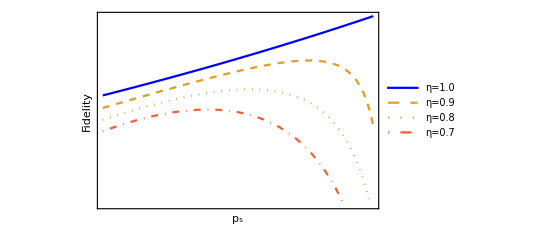

```mathematica
Plot[
{Fr[β,p1,d,0.0],
Fr[β,p1,d,0.1],
Fr[β,p1,d,0.2],
Fr[β,p1,d,0.3]},
{p1,0,1},
Frame->True,FrameLabel->{"p_s","Fidelity"},RotateLabel->True,FrameStyle->Directive[Black],
FrameTicks->{{None,All},{None,All}},
PlotLegends->Placed[LineLegend[{"η=1.0","η=0.9","η=0.8","η=0.7"},LegendLayout->{"Row",2}],{Left,Bottom}],
PlotStyle->{Blue, Dashed, Dotted, DotDashed},
BaseStyle->{FontFamily->"Times",FontSize->12}
]
```

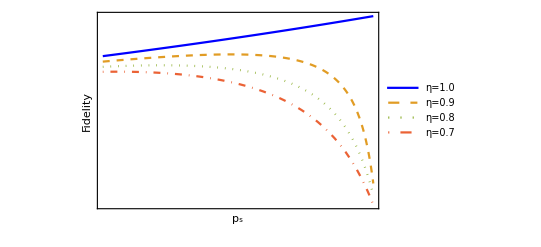

```mathematica
Plot[
{Fr[β,p1,d,0.0],
Fr[β,p1,d,0.1],
Fr[β,p1,d,0.2],
Fr[β,p1,d,0.3]},
{p1,0,1},
Frame->True,FrameLabel->{"p_s","Fidelity"},RotateLabel->True,FrameStyle->Directive[Black],
FrameTicks->{{None,All},{None,All}},
PlotLegends->Placed[LineLegend[{"η=1.0","η=0.9","η=0.8","η=0.7"},LegendLayout->{"Row",2}],{Left,Bottom}],
PlotStyle->{Blue, Dashed, Dotted, DotDashed},
BaseStyle->{FontFamily->"Times",FontSize->12}
]
```